```mathematica
c0 [g_,o_]:=2g^(3/2)(Sqrt[Pi]/4Erf[o/Sqrt[g]](2o^2/g+1) + o/Sqrt[g]Exp[-o^2/g] /2+ Sqrt[Pi]/4(1+2o^2/g))/Pi
```

```mathematica
c2[g_,o_]:= Sqrt[Pi g](1 + Erf[o/Sqrt[g]])/Pi
```

```mathematica
g = 1.1;
o = 1 -3g/2;
wl = Table[w,{w,0,5,.1}];
(*t=Table[NIntegrate[x^3 Exp[-(Abs[x]-o)^2/g]/(x- w),{x,-Infinity,w,Infinity},Method->PrincipalValue],{w,0,5,1}]*)
```

```mathematica
u=Table[NIntegrate[x^3Exp[-(RealAbs[x]-o)^2/g]/(x-w) ,{x,-Infinity,w,Infinity},Method->PrincipalValue]/Pi,{w,0,10,.1}];
```

```mathematica
w2 = Table[w,{w,0,10,.1}];
```

```mathematica
Manipulate[Show[{ListPlot[Transpose[{w2, u }],Joined->True,PlotRange->Full],Plot[(c0[g,o]+c2[g,o]w^2-4c2[g,o] w^4)/(1 +(c2[g,o] /c0[g,o])^2 w^6),{w,0,10},PlotStyle->Orange,PlotRange->Full]},GridLines->{{a,b},{}},PlotRange->Full],{a,0,5},{b,0,6}]
```

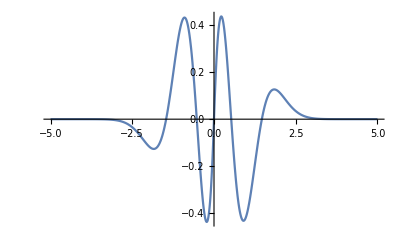

```mathematica
Plot[D[x^3 Exp[-(RealAbs[x]-o)^2/g],{x,2}]/.x->y,{y,-5,5}]
```

```mathematica
NSolve[D[x^3 Exp[-(RealAbs[x]-o)^2/g],{x,2}]==0,x]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-1.46384},{x→-0.527018},{x→0},{x→0.527018},{x→1.46384}}